# MyNeuralNetworkStuff

```mathematica
InitializeNetwork[layerarchitecture_]:=
Module[{w,d,x,L},
L=Length[layerarchitecture];
For[i=0,i< L,i++,
d[i]=layerarchitecture[[i+1]];
];
For[l=1,l≤L,l++,
For[j=1,j≤d[l],j++,
For[i=0,i≤d[l-1],i++,
(w[l][i][j])=RandomReal[{-1,1}];
];
];
];
{w,d,L-1,x}]
```

```mathematica
ComputeOutput[{w_,d_,L_,x_},inputs_]:=
Module[{},
x[0][0]=1;
For[j=1,j≤d[0],j++,
x[0][j]=inputs[[j]];
];
For[l=1,l≤ L,l++,
x[l][0]=1;
For[j=1,j≤ d[l],j++,
x[l][j]=Tanh[Sum[w[l][i][j]*x[l-1][i],{i,0,d[l-1]}]];
];
];
Table[x[L][j],{j,1,d[L]}]
]
```

```mathematica
Learn[{w_,d_,L_,x_},inputs_,outputs_,numSamples_,numIter_,alpha_]:=
Module[{delta,y,k},
For[iter=0,iter<numIter,iter++,
k=RandomInteger[{1,numSamples}];
ComputeOutput[{w,d,L,x},inputs[[(k-1)*(d[0])+1;;((k)*(d[0]))]]];
y[0]=1;
For[j=1,j≤ d[L],j++,
y[j]=outputs[[(k-1)*(d[L])+j]];
];
For[j=1,j≤d[L],j++,
(delta[L][j])=(1-(x[L][j])^2)*(x[L][j]-y[j]);
];
For[l=L,l≥1,l--,
For[i=1,i≤d[l-1],i++,
(delta[l-1][i])=(1-(x[l-1][i])^2)*Sum[((w[l][i][j])*(delta[l][j])),{j,1,d[l]}];
];
];
For[l=1,l≤L,l++,
For[j=1,j≤d[l],j++,
For[i=0,i≤d[l-1],i++,
(w[l][i][j])=(w[l][i][j])-alpha*(x[l-1][i])*(delta[l][j]);
];
];
];
];
{w,d,L,x}
]
```

```mathematica
titi[1][2][4]=RandomReal[{1,3}]
```

1.21137

# Usage

## Xor problem, centered on (0,0)

```mathematica
inputs={{-1,1},{1,-1},{1,1},{-1,-1}};
outputs={{1},{1},{-1},{-1}};
```

```mathematica
network=InitializeNetwork[{2,3,1}];
```

```mathematica
Button["Iterate",network=Learn[network,Flatten[inputs],Flatten[outputs],Length[inputs],1,0.1]]
```

Iterate

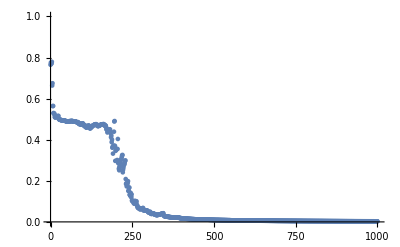

```mathematica
ListPlot[Table[{iter,(network=Learn[network,Flatten[inputs],Flatten[outputs],Length[inputs],1,0.1];Sum[(outputs[[i]][[1]]-ComputeOutput[network, inputs[[i]]][[1]])^2/(Length[inputs]*2),{i,1,Length[inputs]}])},{iter,0,1000}],PlotRange->{0,1}]
```

```mathematica
Show[Plot3D[ComputeOutput[network, {x,y}][[1]],{x,-1,1},{y,-1,1}],
ListPointPlot3D[Table[{inputs[[i]][[1]],inputs[[i]][[2]],outputs[[i]][[1]]},{i,1,Length[inputs]}]],PlotRange->All]
```

-Graphics3D-

## Cross problem, centered on (0,0)

```mathematica
inputs=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{i,1,50}];
outputs=Table[{If[Abs[inputs[[i]][[1]]]>0.3&&Abs[inputs[[i]][[2]]]≥0.3,1,-1 ]},{i,1,Length[inputs]}];
```

```mathematica
network=InitializeNetwork[{2,4,1}];
```

```mathematica
Button["Iterate",network=Learn[network,Flatten[inputs],Flatten[outputs],Length[inputs],1,0.1]]
```

Iterate

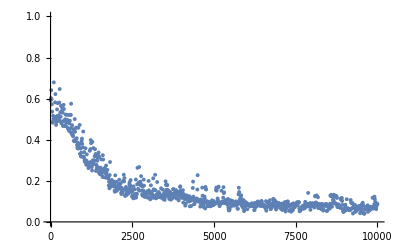

```mathematica
ListPlot[Table[{iter,(network=Learn[network,Flatten[inputs],Flatten[outputs],Length[inputs],10,0.1];Sum[(outputs[[i]][[1]]-ComputeOutput[network, inputs[[i]]][[1]])^2/(Length[inputs]*2),{i,1,Length[inputs]}])},{iter,0,10000,10}],PlotRange->{0,1}]
```

```mathematica
Show[Plot3D[ComputeOutput[network, {x,y}][[1]],{x,-1,1},{y,-1,1}],
ListPointPlot3D[Table[{inputs[[i]][[1]],inputs[[i]][[2]],outputs[[i]][[1]]},{i,1,Length[inputs]}]],PlotRange->All]
```

-Graphics3D-